```mathematica
Print@Names["paul`*"]
```

```mathematica
Graphics3D[{ImportObjVC@"rgb triangle.obj"},Lighting->{{"Ambient",White}}]
Graphics3D[{EdgeForm[None],ImportObjVC@"sokrates.obj"},Lighting->{{"Ambient",White}}]
```

-Graphics3D-

```mathematica
Quit
```

```mathematica
??Parallel`*`*
```

Parallel`VirtualShared`Private`$thisFile

Parallel`VirtualShared`Private`$thisFile=C:\Program Files\Wolfram Research\Mathematica\10.4\AddOns\Applications\Parallel\VirtualShared.m

```mathematica
StartScheduledTask@CreateScheduledTask[a++,{0.}]
```

```mathematica
a=0
SetSharedVariable[a]
ParallelEvaluate[StartScheduledTask@CreateScheduledTask[a++,{0.}]]
Dynamic@a
```

0

{Parallel`Client`CallBackPacket[a++],Parallel`Client`CallBackPacket[a++],Parallel`Client`CallBackPacket[a++],Parallel`Client`CallBackPacket[a++]}

```mathematica
ParallelSubmitTo~SetAttributes~HoldFirst
ParallelSubmitTo[e_,k_]:=(ParallelEvaluate[
StartScheduledTask@CreateScheduledTask[e,{0.}]
,k];Null)
ParallelSubmitTo[Print@$KernelID,First@Kernels[]]
```

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
<<paul`
LaunchKernels[]
Kernels[]
Parallel`Developer`KernelStatus[]
ParallelEvaluate[$KernelID]
Parallel`Settings`$MathLinkTimeout=40
Do[

ParallelSubmit[
Pause[1];Print@$KernelID
];
Pause[0.02]

,6]
```

$Failed

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

{1,2,3,4}

40

```mathematica
Do[
ParallelSubmit[Pause[0.1];Print@$KernelID]
,100]
```

```mathematica
$FrontEnd
```

```mathematica
Quit
```

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
Module[{a},
SetSharedVariable[a];
Do[

ParallelSubmit[
Pause[1];Print@{a=Disk[]};Print@$KernelID
];
Parallel`Developer`QueueRun[];
Pause[0.002];
Parallel`Developer`QueueRun[];

,20]
]
```

```mathematica
<<paul`

a=1
oo:=

ColorSlider[Dynamic[col,{(col=#1)&,(col=#1;oo)&}]]
```

1

$CellContext`col

{1,Disk[{0,0}]}

{1,Disk[{0,0}]}

4

3

{1,Disk[{0,0}]}

{1,Disk[{0,0}]}

2

1

{1,Disk[{0,0}]}

2

{1,Disk[{0,0}]}

1

{1,Disk[{0,0}]}

4

{1,Disk[{0,0}]}

3

{1,Disk[{0,0}]}

2

{1,Disk[{0,0}]}

1

```mathematica
oldlinks=Links[];
LaunchKernels[]
subkernellinks=Links[]~Complement~oldlinks
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

{LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…]}

```mathematica
LaunchKernels[]
```

$Failed

```mathematica
Quit
```

```mathematica
<<paul`
Parallel`Developer`KernelStatus[]
Module[{rrUp,col,rr=Point@{0,0}},

rrUp[]:=(
SetSharedVariable[col];
rr~ParallelSubmitPlaceholder~(Pause[2])
);

Column@{
ColorSlider[Dynamic[col,{(col=#1)&,(col=#1;rrUp[])&}]]
,Dynamic[Graphics@rr,TrackedSymbols:>{rr}]
}
]
```

| 
 | 
 | Select Columns...Kernel Configuration...

$CellContext`col$18762

```mathematica
<<paul`
Parallel`Developer`KernelStatus[]
Module[{rrUp,col,rr=Point@{0,0}},

rrUp[]:=(
SetSharedVariable[col];
rr~ParallelSubmitPlaceholder~(Pause[2];{col,Disk[]})
);

Column@{
ColorSlider[Dynamic[col,{(col=#1)&,(col=#1;rrUp[])&}]]
,Dynamic[Graphics@rr,TrackedSymbols:>{rr}]
}
]
```

| 
 | 
 | Select Columns...Kernel Configuration...

$CellContext`col$17633

```mathematica
Do[

ParallelSubmit[
Pause[1];Print@$KernelID
];
Pause[0.02]

,6]
```

```mathematica
LaunchKernels[]
```

```mathematica
Module[{crr},With[{crr=crr},
ParallelSubmitPlaceholder[(Pause[2];Disk[]),crr,Rectangle[]];
ParallelSubmitPlaceholder[(Pause[2];Disk[]),crr,Rectangle[]];

Manipulate[
Graphics@crr(*put Dynamic or:*)
,{x,0,10},LocalizeVariables->False,TrackedSymbols->{crr}(*All*)
]
]]
```

EvaluationObject[41,Set[paul`Private`output$17415,CompoundExpression[Pause[2],Disk[]]],Null,Parallel`Concurrency`Private`state$17416]

paul`Private`output$17415=(Pause[2];«1»)

```mathematica
ParallelSubmitPlaceholder2~SetAttributes~HoldAll

ParallelSubmitPlaceholder2[expr_,placeholder_,whenDone_: Null(*does not seem to work*)]:=Module[{o,w,output,done=False},
o=output;
SetSharedVariable[output];
output=placeholder;
w=ParallelSubmit[output=expr];
Assert[Head@w===EvaluationObject];
(*progress message& make sure whenDone is called*)Print@Dynamic@If[ParallelSubmitFinishedQ[w],If[!done,done=True;whenDone];
{"done",Short@HoldForm@expr},ParallelSubmitGet[w]];

o
];
```

```mathematica
r=ParallelSubmitPlaceholder2[(Pause[2];Disk[]),rr,Rectangle[]]
Dynamic@ParallelSubmitPlaceholder2
```

$CellContext`col

```mathematica
<<paul`;
```

$CellContext`col

$CellContext`col$31200

```mathematica
(*simulate slow graphics*)
ParallelSubmitPlaceholder[(Pause[2];Disk[]),r,Rectangle[]]
Dynamic@Graphics@r
```

```mathematica
(*pointing outwards in 2d note that the color along a given line from the center is constant*)
(*2D normal maps are enough to reconstruct 3D normals, c.f. formula for unit sphere normal map*)
ListNormalVectorPlot@Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.01]

(*pointing to {x,y,1}. Now there is much more blue*)
ListNormalVectorPlot@Map[#~Append~1&,Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.01],{2}]

(*unit sphere normal map, c.f. https://www.filterforge.com/filters/6487-normal.html *)
(*note: the colors at the outline correspond to that in the first picture*)
<<numerics`
ListNormalVectorPlot@Map[
If[1-Norm2@#<0
,{0,0,0}1.
,#~Append~Sqrt[1-Norm2@#](*extend to unit normal/point on unit sphere*)
]&,

Transpose@CoordinateBoundsArray[Table[{-1,1},2],0.005],

{2}
]
```

-Graphics-

-Graphics-

-Graphics-

{{0.621256,0.382281,-0.0485134,0.757376,0.591709,-0.0479351,-0.213449,-0.344703,0.62098,0.504475},{0.486827,0.924124,-0.655096,0.0548844,0.423053,0.186515,-0.63956,-0.185881,0.342784,0.706804},{0.0537286,-0.234407,-0.0668476,0.51005,0.556852,-0.919359,-0.332206,0.54001,0.0221519,0.191673},{-0.202167,-0.448763,0.366911,0.350453,-0.353576,-0.963106,-0.931426,-0.455872,-0.678936,-0.9032}}

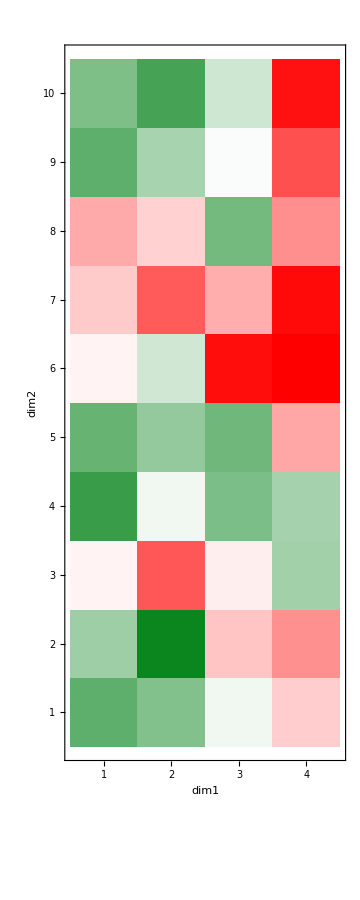
-Graphics-MatrixPlot

{Speed,Quality}

```mathematica
m=RandomReal[{-1,1},{4,10}]
ShowDistanceField[m,Method->MatrixPlot]~Labeled~MatrixPlot
Labeled[ShowDistanceField[m,PerformanceGoal->#],#]&/@{"Speed","Quality"}
```

```mathematica
(*demo*)
m=Table[
Sin[3.x]Sin[3.y]Sin[3.z]-0.5
,{x,0.,3.,0.1},{y,0.,3.,0.1},{z,-1.,1.,0.1}];
m=Table[x-5,{x,10},{y,4},{z,6}](**)(*dim1,dim2,dim3*);
m=RandomReal[{-1,1},{10,4,6}];
$PrePrint=.;
{ShowDistanceField3DSlice[m,Method->MatrixPlot]~Labeled~ShowDistanceField3DSlice[MatrixPlot]}~Join~
(ShowDistanceField3DSlice[m,PerformanceGoal->#]~Labeled~ShowDistanceField3DSlice[#]&/@{"Speed","Quality"})

{ShowDistanceField3D[m,Method->Image3D]~Labeled~Image3D}~Join~(ShowDistanceField3D[m,PerformanceGoal->#]~Labeled~#&/@{"Speed","Quality"(*,"HighQuality"*)})
```

{ShowDistanceField3DSlice[MatrixPlot],ShowDistanceField3DSlice[Speed],ShowDistanceField3DSlice[Quality]}

{-Graphics3D-Image3D,Speed,Quality}